## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`';
Get["MASSef`"];
Get["MASSef`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="GAPD";
fitLabel=rxnName;
dataFileName=rxnName;
KeqEquilibrator=0.408;

assumedUncertaintyFraction = 0.05;
removeInputFiles = False;
removeOutputFiles = True;
(* user will need to change this path *)
pathMASSFittingPackage = "/home/mrama/Dropbox/test bla/MASSef/";

mainFolder = "fit_dKd_GAPD";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data.csv"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.csv"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.csv"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath, assumedUncertaintyFraction];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

```mathematica
printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Km Values:

Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
g3p | 0.00089 | 0.0008455
0.0009345 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 | M | 8.9 | 22 | teoa | 0.04 |

### Construct enzyme module

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi
"[nad,g3p,pi,1,3-diphosphoglycerate,nadh]"

```mathematica
catalyticBranch={"E_GAPD[c] + nad[c] <=> E_GAPD[c]&nad",
				"E_GAPD[c]&nad + g3p[c] <=> E_GAPD[c]&nad&g3p",
				"E_GAPD[c]&nad&g3p + pi[c] <=> E_GAPD[c]&nad&g3p&pi",
				"E_GAPD[c]&nad&g3p&pi <=> E_GAPD[c]&nadh&13dpg",
				"E_GAPD[c]&nadh&13dpg <=> E_GAPD[c]&nadh + 13dpg[c]",
				"E_GAPD[c]&nadh<=> E_GAPD[c] + nadh[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->2,Inhibitors->{},InhibitionSites->0];
```

```mathematica
enzymeModel["Reactions"]
```

{((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,((GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c)^GAPD2,((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,((GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c)^GAPD4,((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6}

### Setup King-Altmann Equations

```mathematica
{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;
simplifyMaxTime=1*^-5;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
eqRateConstSub={};


(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
simplifyMaxTime = 100; (*in seconds*)
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs, simplifyMaxTime, nActiveSites];


(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getEquivRateConsts[enzymeModel, eqRateConstSub, nonCatalyticReactions];

(*Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data*)
(*Simplify fixes Python evaluation issues dealing with fractional exponents (e.g.'(-1)**(3/5)' returns 1.0)*)
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub];


(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];
```

{}

## Semi-Automated Simulate Data

### User Input Section

```mathematica
logStepSize=0.2;
(*nonKmParamWeight=3;*)
(*Weighting factor for non-Km data points. You can be specify this manually*)
{minPsDataVal, maxPsDataVal}= getMinMaxPsDataVal[1];
nonKmParamWeight=Length[Table[1,{i,minPsDataVal, maxPsDataVal,logStepSize}]];
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)
```

### Simulate data

```mathematica
otherParmsList
```

{{Kd,nad,3.2×10^-7,{2.5×10^-7,3.9×10^-7},M,8.9,22,{{teoa,0.04}},{}}}

```mathematica
pHandT={8.9, 22};

kmFittingData= simulateKmData[rxn, metsFull,  metSatForSub, metSatRevSub, kmList, otherParmsList, assumedSaturatingConc, eTotal,
			   logStepSize,activeIsoSub, bufferInfo, ionCharge, inputPath,  fileList, KeqEquilibrator];


kcatFittingData=simulateKcatData[rxn, metsFull,  metSatForSub, metSatRevSub, kcatList, otherParmsList, assumedSaturatingConc, eTotal,
			  logStepSize, nonKmParamWeight, activeIsoSub, bufferInfo, ionCharge, inputPath, 
			  fileList, KeqEquilibrator];


haldane=haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
haldaneRatio=haldane[[2]];

{KeqFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[haldaneRatio,KeqEquilibrator, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT,"haldaneRatio"];


KdRatio=Subscript[k, GAPD1]^⟵/Subscript[k, GAPD1]^⟶;
KdVal=otherParmsList[[1]][[3]];
{KdFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[KdRatio,KdVal, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT, "KdRatio"];


dKdVal =4.25*10^2(*1.92*10^4*);
dKdRatio =(Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵);

{dKdFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[dKdRatio,dKdVal, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT, eqnName="dKdRatio"];
```

### Assemble and export All Data

```mathematica
header=Join[Map[ToString, metsSub[[All,1]]],{"FileFlag", "Target_Data"}];

fittingData = Flatten[{kmFittingData,kcatFittingData, KdFittingData,KeqFittingData,dKdFittingData}, 1];

dataPath =FileNameJoin[{inputPath,dataFileName <>".dat"}, OperatingSystem->$OperatingSystem];

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
FilePrint[dataPath]
```

Keq_GAPD	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0.408	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0.408	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0.408	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0.408	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0.408	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0.408	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0.408	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0.408	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0.408	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0.408	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0.408	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0.408	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0.408	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0.408	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0.408	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0.408	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0.408	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0.408	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0.408	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0.408	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0.408	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0.408	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0.408	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0.408	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0.408	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0.408	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0.408	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0.408	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.5
0.408	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0.408	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0.408	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0.408	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0.408	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=1;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	1
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python","\""<>runFitScriptPath <>"\"", "\""<>psoParameterPath <>"\"", "\""<>lmaParameterPath <>"\"", "\""<>psoTrialSummaryFileName <>"\"","\""<> psoResultsFileName <>"\"", "\""<>lmaResultsFileName <>"\"", ToString @numTrials, "\""<>dataPath <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"]
```

best_fit: 1.09774120267

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
splitChar = If[$OperatingSystem == "Windows", "\\", "/"];
resultsFileName = StringSplit[lmaResultsFileName, splitChar][[-1]];
fittingData = Import[FileNameJoin[{inputPath, dataFileName<>".dat"}, OperatingSystem->$OperatingSystem]];
fittingData = fittingData[[2;;,All]];
resultsFile = FileNameJoin[{"raw",resultsFileName}, OperatingSystem->$OperatingSystem];
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,fitLabel];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  | 
relRateFor_nad | 0.0283688 | 0.000804788 | 6.75022 | 0.0909091 | 0.0970457
relRateFor_nad | 0.0268912 | 0.000723138 | 6.38765 | 0.136807 | 0.145546
relRateFor_nad | 0.0248408 | 0.000617063 | 5.88654 | 0.20076 | 0.212578
relRateFor_nad | 0.0221626 | 0.000491179 | 5.23557 | 0.284747 | 0.299655
relRateFor_nad | 0.0189284 | 0.000358284 | 4.4548 | 0.386863 | 0.404097
relRateFor_nad | 0.0153731 | 0.000236331 | 3.60317 | 0.5 | 0.518016
relRateFor_nad | 0.0118466 | 0.000140342 | 2.76532 | 0.613137 | 0.630092
relRateFor_nad | 0.00868806 | 0.0000754823 | 2.02064 | 0.715253 | 0.729705
relRateFor_nad | 0.00610736 | 0.0000372999 | 1.41621 | 0.79924 | 0.810559
relRateFor_nad | 0.00415249 | 0.0000172432 | 0.960732 | 0.863193 | 0.871486
relRateFor_nad | 0.00275493 | 7.58963×10^-6 | 0.636362 | 0.909091 | 0.914876
relRateFor_g3p | 0.101806 | 0.0103645 | 26.4172 | 0.0909091 | 0.114925
relRateFor_g3p | 0.096052 | 0.00922598 | 24.7533 | 0.136807 | 0.170671
relRateFor_g3p | 0.0881594 | 0.00777208 | 22.5066 | 0.20076 | 0.245944
relRateFor_g3p | 0.0780076 | 0.00608518 | 19.6761 | 0.284747 | 0.340775
relRateFor_g3p | 0.0659758 | 0.00435281 | 16.4061 | 0.386863 | 0.450332
relRateFor_g3p | 0.0530236 | 0.0028115 | 12.9857 | 0.5 | 0.564929
relRateFor_g3p | 0.0404465 | 0.00163592 | 9.76061 | 0.613137 | 0.672983
relRateFor_g3p | 0.0293991 | 0.000864304 | 7.00376 | 0.715253 | 0.765347
relRateFor_g3p | 0.0205189 | 0.000421024 | 4.83803 | 0.79924 | 0.837907
relRateFor_g3p | 0.0138767 | 0.000192562 | 3.24681 | 0.863193 | 0.891219
relRateFor_g3p | 0.00917154 | 0.0000841171 | 2.13428 | 0.909091 | 0.928493
relRateFor_pi | 0.15404 | 0.0237284 | 29.8609 | 0.0909091 | 0.0637628
relRateFor_pi | 0.147443 | 0.0217394 | 28.7873 | 0.136807 | 0.0974238
relRateFor_pi | 0.13808 | 0.019066 | 27.2354 | 0.20076 | 0.146082
relRateFor_pi | 0.125469 | 0.0157425 | 25.0915 | 0.284747 | 0.2133
relRateFor_pi | 0.109626 | 0.0120178 | 22.3084 | 0.386863 | 0.30056
relRateFor_pi | 0.0913703 | 0.00834853 | 18.973 | 0.5 | 0.405135
relRateFor_pi | 0.0723136 | 0.00522925 | 15.3384 | 0.613137 | 0.519091
relRateFor_pi | 0.0543644 | 0.00295549 | 11.7661 | 0.715253 | 0.631096
relRateFor_pi | 0.0390247 | 0.00152293 | 8.59387 | 0.79924 | 0.730554
relRateFor_pi | 0.0269696 | 0.000727358 | 6.02109 | 0.863193 | 0.81122
relRateFor_pi | 0.0181069 | 0.000327858 | 4.08354 | 0.909091 | 0.871968
absRateFor | 3.09795×10^-6 | 9.5973×10^-12 | 0.000713327 | 268 | 267.998
absRateFor | 3.09795×10^-6 | 9.5973×10^-12 | 0.000713327 | 268 | 267.998
absRateFor | 3.09795×10^-6 | 9.5973×10^-12 | 0.000713327 | 268 | 267.998
absRateFor | 3.09795×10^-6 | 9.5973×10^-12 | 0.000713327 | 268 | 267.998
absRateFor | 3.09795×10^-6 | 9.5973×10^-12 | 0.000713327 | 268 | 267.998
absRateFor | 3.09795×10^-6 | 9.5973×10^-12 | 0.000713327 | 268 | 267.998
absRateFor | 3.09795×10^-6 | 9.5973×10^-12 | 0.000713327 | 268 | 267.998
absRateFor | 3.09795×10^-6 | 9.5973×10^-12 | 0.000713327 | 268 | 267.998
absRateFor | 3.09795×10^-6 | 9.5973×10^-12 | 0.000713327 | 268 | 267.998
absRateFor | 3.09795×10^-6 | 9.5973×10^-12 | 0.000713327 | 268 | 267.998
absRateFor | 3.09795×10^-6 | 9.5973×10^-12 | 0.000713327 | 268 | 267.998
KdRatio | 0.326789 | 0.106791 | 112.221 | 3.2×10^-7 | 6.79108×10^-7
KdRatio | 0.326789 | 0.106791 | 112.221 | 3.2×10^-7 | 6.79108×10^-7
KdRatio | 0.326789 | 0.106791 | 112.221 | 3.2×10^-7 | 6.79108×10^-7
KdRatio | 0.326789 | 0.106791 | 112.221 | 3.2×10^-7 | 6.79108×10^-7
KdRatio | 0.326789 | 0.106791 | 112.221 | 3.2×10^-7 | 6.79108×10^-7
KdRatio | 0.326789 | 0.106791 | 112.221 | 3.2×10^-7 | 6.79108×10^-7
KdRatio | 0.326789 | 0.106791 | 112.221 | 3.2×10^-7 | 6.79108×10^-7
KdRatio | 0.326789 | 0.106791 | 112.221 | 3.2×10^-7 | 6.79108×10^-7
KdRatio | 0.326789 | 0.106791 | 112.221 | 3.2×10^-7 | 6.79108×10^-7
KdRatio | 0.326789 | 0.106791 | 112.221 | 3.2×10^-7 | 6.79108×10^-7
KdRatio | 0.326789 | 0.106791 | 112.221 | 3.2×10^-7 | 6.79108×10^-7
haldaneRatio | 0.0019899 | 3.95969×10^-6 | 0.457143 | 0.408 | 0.406135
haldaneRatio | 0.0019899 | 3.95969×10^-6 | 0.457143 | 0.408 | 0.406135
haldaneRatio | 0.0019899 | 3.95969×10^-6 | 0.457143 | 0.408 | 0.406135
haldaneRatio | 0.0019899 | 3.95969×10^-6 | 0.457143 | 0.408 | 0.406135
haldaneRatio | 0.0019899 | 3.95969×10^-6 | 0.457143 | 0.408 | 0.406135
haldaneRatio | 0.0019899 | 3.95969×10^-6 | 0.457143 | 0.408 | 0.406135
haldaneRatio | 0.0019899 | 3.95969×10^-6 | 0.457143 | 0.408 | 0.406135
haldaneRatio | 0.0019899 | 3.95969×10^-6 | 0.457143 | 0.408 | 0.406135
haldaneRatio | 0.0019899 | 3.95969×10^-6 | 0.457143 | 0.408 | 0.406135
haldaneRatio | 0.0019899 | 3.95969×10^-6 | 0.457143 | 0.408 | 0.406135
haldaneRatio | 0.0019899 | 3.95969×10^-6 | 0.457143 | 0.408 | 0.406135
dKdRatio | 9.17826×10^-6 | 8.42405×10^-11 | 0.0021134 | 425. | 425.009
dKdRatio | 9.17826×10^-6 | 8.42405×10^-11 | 0.0021134 | 425. | 425.009
dKdRatio | 9.17826×10^-6 | 8.42405×10^-11 | 0.0021134 | 425. | 425.009
dKdRatio | 9.17826×10^-6 | 8.42405×10^-11 | 0.0021134 | 425. | 425.009
dKdRatio | 9.17826×10^-6 | 8.42405×10^-11 | 0.0021134 | 425. | 425.009
dKdRatio | 9.17826×10^-6 | 8.42405×10^-11 | 0.0021134 | 425. | 425.009
dKdRatio | 9.17826×10^-6 | 8.42405×10^-11 | 0.0021134 | 425. | 425.009
dKdRatio | 9.17826×10^-6 | 8.42405×10^-11 | 0.0021134 | 425. | 425.009
dKdRatio | 9.17826×10^-6 | 8.42405×10^-11 | 0.0021134 | 425. | 425.009
dKdRatio | 9.17826×10^-6 | 8.42405×10^-11 | 0.0021134 | 425. | 425.009
dKdRatio | 9.17826×10^-6 | 8.42405×10^-11 | 0.0021134 | 425. | 425.009

### Simulated Data and Best Fit Data Plot

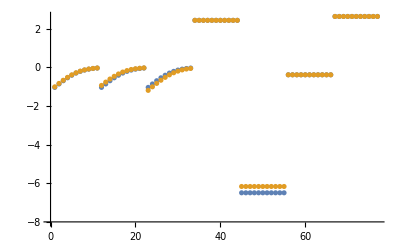

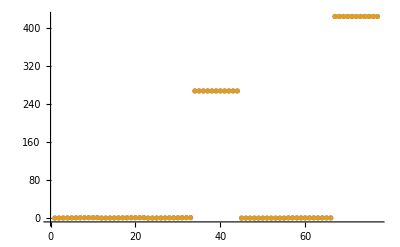

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

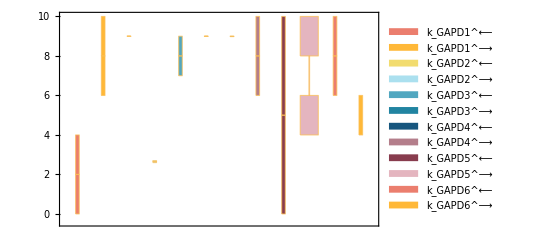

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

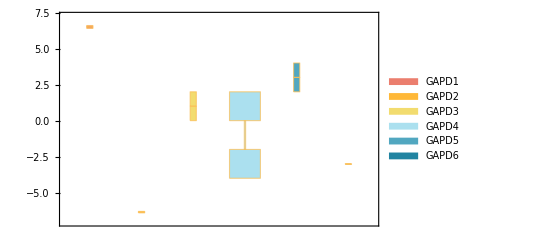

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

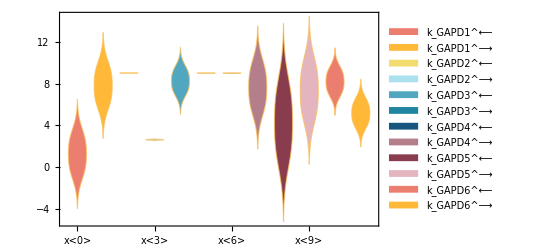

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

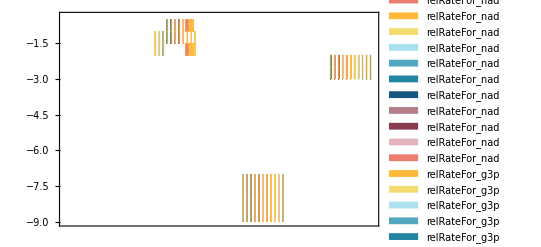

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> eTotal;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.0000418699 | 6.95572
0.00089 | 0.00068542 | 22.9865
0.00053 | 0.000778206 | 46.8313

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 267.998 | 0.000713327

```mathematica
backCalculateRatios[dKdRatio, dKdVal, paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425.009 | 0.0021134